```mathematica
(*idk if i will need these or not*)
(*These functions are to precompute the time integrals*)
(*Compute the partitions of the list x*)
partition[{x_}]:={{{x}}};
partition[{r__,x_}]:=Join@@(ReplaceList[#,{{b___,{S__},a___}:>{b,{S,x},a},{S__}:>{S,{x}}}]&/@partition[{r}]);
```

```mathematica
(*Kimura's eigenvalues*)
KimuraEig[i_]:=1/2*i*(i+1); 
(*The inside of all the time integrals*)
integrand[k_]:=Exp[Sum[( KimuraEig[m[i+1]] - KimuraEig[m[i]] - (2^(1+j[i])* Ne * VG / W))s[i],{i,1,k}]];
```

```mathematica
(*lets see what the inside of a 3 fold time integral would look like*)
k=3
integrand[k]
```

3

ⅇ^((-(2^(1+j[1]) Ne VG)/W-1/2 m[1] (1+m[1])+1/2 m[2] (1+m[2])) s[1]+(-(2^(1+j[2]) Ne VG)/W-1/2 m[2] (1+m[2])+1/2 m[3] (1+m[3])) s[2]+(-(2^(1+j[3]) Ne VG)/W-1/2 m[3] (1+m[3])+1/2 m[4] (1+m[4])) s[3])

```mathematica
integrand[k] /. {m[1 ]->m[2], VG ->1}
```

ⅇ^(-(2^(1+j[1]) Ne s[1])/W+(-(2^(1+j[2]) Ne)/W-1/2 m[2] (1+m[2])+1/2 m[3] (1+m[3])) s[2]+(-(2^(1+j[3]) Ne)/W-1/2 m[3] (1+m[3])+1/2 m[4] (1+m[4])) s[3])

```mathematica
sLimits[k_] := Join[{{s[k],0,t}},Reverse[Table[{s[j],0,s[j+1]},{j,1,k-1}]]];
sLimits[k]
```

{{s[3],0,t},{s[2],0,s[3]},{s[1],0,s[2]}}

```mathematica
Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]]
```

(8 W^3 (1/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4]))))-1/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(2^(2+j[1]) Ne VG+W (m[1]+m[1]^2-m[2] (1+m[2])))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4]))))+ⅇ^(-(t (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4]))))/(2 W)) (-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]) Ne VG)/W+m[1]+m[1]^2-m[3] (1+m[3]))))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4]))))+(ⅇ^(-1/2 t ((2^(2+j[2]) Ne VG)/W+m[2]+m[2]^2-m[3] (1+m[3]))))/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(-2^(2+j[1]) Ne VG+W (-m[1]-m[1]^2+m[2]+m[2]^2))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4])))))))/(2^(2+j[1]) Ne VG+W (m[1]+m[1]^2-m[2] (1+m[2])))

```mathematica
Integrate[integrand[k]/. {m[1 ]->m[2], VG ->1},Evaluate[Sequence@@sLimits[k]]]
```

1/Ne 2^(1-j[1]) W^3 ((ⅇ^(-1/2 t ((4 (2^j[2]+2^j[3]) Ne)/W+m[2]+m[2]^2-m[4] (1+m[4]))))/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]+2^j[3]) Ne)/W+m[2]+m[2]^2-m[4] (1+m[4]))))/((4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(2^(2+j[1]) ⅇ^(-1/2 t ((2^(2+j[3]) Ne)/W+m[3]+m[3]^2-m[4] (1+m[4]))) Ne)/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4]))))+(2^(2+j[1]) Ne)/((4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4])))))

```mathematica
Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]] /. {m[1 ]->m[2], VG ->1}
```

(4 W^2 (-2 W (1/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-1/((4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(2^(2+j[1]) Ne)/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4])))))+2 ⅇ^(-(t (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4]))))/(2 W)) W ((ⅇ^(-1/2 t ((2^(2+j[2]) Ne)/W+m[2]+m[2]^2-m[3] (1+m[3]))))/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]) Ne)/W+m[2]+m[2]^2-m[3] (1+m[3]))))/((4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(2^(2+j[1]) Ne)/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4])))))))/(2^(2+j[1]) Ne+W (m[2]+m[2]^2-m[2] (1+m[2])))

```mathematica
a = Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]] /. {m[1 ]->m[2], VG ->0} 
b = Integrate[integrand[k]/. {m[1 ]->m[2], VG ->0},Evaluate[Sequence@@sLimits[k]]]
```

0

1/((m[2]-m[3])^2 (1+m[2]+m[3])^2)((8 (-2 m[2]-2 m[2]^2+m[3]+m[3]^2+m[4]+m[4]^2))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)+8/(m[3]+m[3]^2-m[4] (1+m[4]))+ⅇ^(-1/2 t (m[2]-m[4]) (1+m[2]+m[4])) ((4 t (m[2]+m[2]^2-m[3] (1+m[3])))/((m[2]-m[4]) (1+m[2]+m[4]))+(8 (2 m[2]+2 m[2]^2-m[3]-m[3]^2-m[4] (1+m[4])))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)-(8 ⅇ^(1/2 t (m[2]-m[3]) (1+m[2]+m[3])))/(m[3]+m[3]^2-m[4] (1+m[4]))))

```mathematica
FullSimplify[a == b]
```

1/((m[2]-m[3])^2 (1+m[2]+m[3])^2)((8 (-2 m[2] (1+m[2])+m[3]+m[3]^2+m[4]+m[4]^2))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)+8/(m[3]+m[3]^2-m[4] (1+m[4]))+ⅇ^(-1/2 t (m[2]-m[4]) (1+m[2]+m[4])) ((4 t (m[2]-m[3]) (1+m[2]+m[3]))/((m[2]-m[4]) (1+m[2]+m[4]))-(8 ⅇ^(1/2 t (m[2]-m[3]) (1+m[2]+m[3])))/(m[3]+m[3]^2-m[4] (1+m[4]))+(16 m[2] (1+m[2])-8 (m[3]+m[3]^2+m[4]+m[4]^2))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)))==0

```mathematica
(*Define the limits of the k fold sum over the j_i s *)
jLimits[k_] := Table[{j[i],0,1},{i,1,k}];
jLimits[k]
```

{{j[1],0,1},{j[2],0,1},{j[3],0,1}}

```mathematica
(*Define the limits of the k+1 fold infinite sums. Truncating after n_ terms*)
mLimits[k_, n_ ] := Join[{{m[1],1,n}},Table[{m[j],m[j-1]-2,m[j-1]+2,1},{j,2,k+1}]];
n = 20;
```

```mathematica
mLimits[k,n]
```

{{m[1],1,20},{m[2],-2+m[1],2+m[1],1},{m[3],-2+m[2],2+m[2],1},{m[4],-2+m[3],2+m[3],1}}

```mathematica
(*We can precompute the integrral over time for a given k.*)
computeTimeInts[k_] :=  Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]];
```

```mathematica
computeTimeInts[k]
```

(4 W^2 (-2 W (-1/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4]))))+1/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(-2^(2+j[1]) Ne VG+W (-m[1]-m[1]^2+m[2]+m[2]^2))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4])))))+2 ⅇ^(-(t (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4]))))/(2 W)) W (-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]) Ne VG)/W+m[1]+m[1]^2-m[3] (1+m[3]))))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4]))))+(ⅇ^(-1/2 t ((2^(2+j[2]) Ne VG)/W+m[2]+m[2]^2-m[3] (1+m[3]))))/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(-2^(2+j[1]) Ne VG+W (-m[1]-m[1]^2+m[2]+m[2]^2))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4])))))))/(2^(2+j[1]) Ne VG+W (m[1]+m[1]^2-m[2] (1+m[2])))

```mathematica
integrandPart[myPartition_,k_]:=Module[{curFun,firstElement,block,curElement},
curFun = integrand[k];
 For[a=1,a≤Length[myPartition],a++,
firstElement = myPartition[[a,1]];
For[b=2,b≤Length[myPartition[[a]]],b++,
curElement = myPartition[[a,b]];
curFun = curFun/.m[curElement]->m[firstElement];
];
];
curFun//FullSimplify
]
```

```mathematica
(*TODO think of better names for these functions*)
computeInts[k_]:=Module[{curParts,curLimits,curIntegrand,curInts,j},
curParts = partition[Table[j,{j,1,k+1}]];
curLimits = sLimits[k];
For[j=1,j≤Length[curParts],j++,
curIntegrand=integrandPart[curParts[[j]],k];
curInts[curParts[[j]]]=Integrate[curIntegrand,Evaluate[Sequence@@curLimits]];
];
Return[curInts]
]
```

```mathematica
(*Functions to compute the path integral to order k*)
(*Find the partition given the current state of the summation*)
findEquiv[vals_] := Module[{tempPart},
tempPart=Function[val,Flatten[Position[vals,val]]]/@Union[vals];
Sort[tempPart,Less[First[#1],First[#2]]&]
]
```

```mathematica
(*These functions are to compute the space integrals involving the Gegenbauer functions*)
(*The normalizations for the Gegenbauer polynomials*)
gegenbauerNorm[n_,λ_:3/2] := π*2^(1-2*λ)*Gamma[n+2*λ]/(Factorial[n]*(n+λ)*Gamma[λ]^2);
```

```mathematica
f[0,0]=1;
f[a_,b_]:=a^b
```

```mathematica
(*TODO quadruple check this expression*)
(*Maybe replace this junk with an if statement*)
computeSpaceInt[a_,b_,j_] := 1/(2^(4+j))( KroneckerDelta[a,b]* gegenbauerNorm[a] - 
(f[(1/(3+2a) * 
((a+1)*KroneckerDelta[a,b-1]*gegenbauerNorm[a+1]+
(a+2)*KroneckerDelta[a,b+1]*gegenbauerNorm[a-1])),(1-j) ] * (*3rdd to last partenthesis on this line was missing. check if this fixed*)
f[(1/((2*a+3)*(2*b+3))*
((a+1)*(b+1)*KroneckerDelta[a,b]*gegenbauerNorm[a+1]+
(a+1)*(b+2)*KroneckerDelta[a,b-2]*gegenbauerNorm[a+1]+
(a+2)*(b+1)*KroneckerDelta[a,b+2]*gegenbauerNorm[a-1]+
(a+2)*(b+2)*KroneckerDelta[a,b]*gegenbauerNorm[a-1])),j]))
```

```mathematica
computeSpaceInt[3,2,0]
gegenbauerNorm[2]
```

-5/42

24/7

```mathematica
(*Define the coefficients from Kimura's solution*)
kimuraCoefficient[i_]:= If[i>0,(2*i+1)/(i*(i+1)),0];
```

```mathematica
(*Kimura's neutral transition density*)
(*I pulled the 4x(1-x) into the leading coefficient*)
Kimura[x_,y_,t_,n_]:= Module[{i},Sum[4*(2*i+1)*x*(1-x)/(i*(i+1))*GegenbauerC[i-1,3/2,1-2*x]*GegenbauerC[i-1,3/2,1-2*y]*Exp[-1/2*i*(i+1)*t],{i,1,n}]
]
```

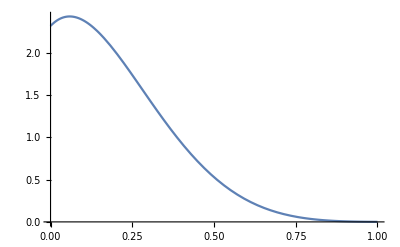

```mathematica
Plot[Kimura[x,y,t,50]/.{x->.2,t->.2},{y,0,1}]
```

```mathematica
Integrate[Kimura[x,y,t,10],{y,0,1}]/. {x->.2,t->.5}
```

0.604253

```mathematica
For[n = 1, n ≤ 20, n ++,
Print[Kimura[x,y,t,n]/.{x->.2,t->.2, y->.4}]
]
```

0.785982

1.1021

0.940175

0.978341

0.952694

0.938279

0.938303

0.937648

0.937601

0.937609

0.937608

0.937608

0.937608

«7 more identical outputs»

```mathematica
kthterm[x_,y_,t_,k_,n_, Ne_, α_, Λ_, W_,VG_] := Module[{kfoldtimeint, mlims, jlims},
mlims = mLimits[k,n];
jlims = jLimits[k];
kfoldtimeint=  computeInts[k];
4 x(1-x)(8 Ne^2 α Λ / W^2)^k* Sum[If[Negative@Min@Table[m[i],{i,1,k+1}], 0, 
GegenbauerC[m[1]-1,3/2,1-2*x]*GegenbauerC[m[k+1]-1,3/2,1-2*y] *Exp[-KimuraEig[m[k+1]*t]]* Product[kimuraCoefficient[m[i]],{i,1,k+1}] * 
Sum[
Product[(2 VG)^(1-j[i])(-α*Λ)^j[i] computeSpaceInt[m[i]-1, m[i+1]-1, j[i]],{i, 1, k}] *
kfoldtimeint[findEquiv[Table[m[i],{i,1,k+1}]]], Evaluate[Sequence@@jlims]]
], Evaluate[Sequence@@mlims]]
]
```

```mathematica
For[i = 1, i ≤10, i++,
Print[GegenbauerC[i-1,3/2,1-2*y]/. {y->0.2}]
]
```

1

1.8

1.2

-0.72

-2.472

-2.39904

-0.234752

2.43994

3.37501

1.56398

```mathematica
k = 3
n = 10
```

3

10

```mathematica
kthterm[x,y,t,k,n,Ne,α,Λ, W, VG]
```

$Aborted

```mathematica
For[k = 1, k ≤ 10, k ++,
Print[kthterm[x,y,t,k,n,Ne,α,Λ, W, VG] /. {x->0.2, t->0.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1, y ->0.4}]
]
```

0.493911

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-802.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.209607

0.0487531

-1.55292

$Aborted

```mathematica
k = 3
(*TODO I think im doubling up on the 8Ne thing. check in the kth term expression*)
approx  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)] * 
(Kimura[x,y,t,n] + 
Sum[kthterm[x,y,t,i,n,Ne,α,Λ, W, VG], {i,1,k}])
```

3

```mathematica
approx /. {x->0.2, t->0.1,Ne->500,α->0.005, Λ -> 1, W->1, VG->0.0004, y ->0.3}
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -0.0542221+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -0.0347176+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
Integrate[approx, {y,0,1}]/. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

TerminatedEvaluation[IterationLimit]

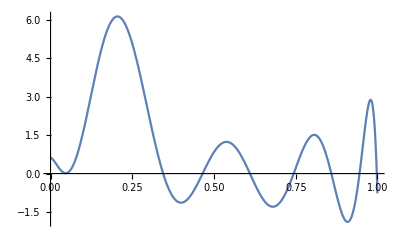

WolframAlphaQueryResults

```mathematica
Plot[approx /. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}, {y,0,1}]
```